# Processing perturbation raw data (experiments and FEM)

## Utils

### General

```mathematica
SetDirectory[NotebookDirectory[]];
githubTextToList[text_String]:=ToExpression[StringReplace[text,{"["->"{","]"->"}"}]];
```

### Plots

```mathematica
(*List RGB color maps*)
listMagma=;
listViridis=;
listBlue=ToExpression@;
listRed=ToExpression@;

(*Color map functions*)
viridisCM=Blend[RGBColor[#]&/@listViridis,#]&;
magmaCM=Blend[RGBColor[#]&/@listMagma,#]&;
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;

optionsListPlot={Joined->True,Frame->True,ImageSize->500,PlotRange->All,BaseStyle->{FontSize->25},LabelStyle->Black,FrameStyle->Directive[Black]};
optionsContourListPlot={Contours->20,ContourShading->True,ContourStyle->None,ColorFunction->magmaCM,ImageSize->500,BaseStyle->{FontSize->25},LabelStyle->Black,FrameStyle->Directive[Black]};
```

## Folder selection: FEM or experiment

```mathematica
pathFEM[node_String]:="../rawData/SSH/FEM - perturbations/20220129_KL_perturbation_output/220129_KL_perturbation_"<>node<>".xlsx"; 
pathFEM4[node_String]:="../rawData/SSH/FEM - perturbations/230213_KL_long_perturbation_N16/230213_KL_long_perturbation_N16.xlsx";
pathFEM5[node_String]:="../rawData/SSH/FEM - perturbations/20230316_KL_ss_perturbation_fix/230315_KL_ss_perturbation_fix_boundaries_"<>node<>".xlsx";
pathEXP[node_String]:="../rawData/SSH/Experiments - perturbations/20220719_KLchain-perturbation/20220719_output_data_"<>node<>".xlsx";
pathEXP2[node_String]:="../rawData/SSH/Experiments - perturbations/20220803_KLchain_defect/outputdata/20220803_output_data_"<>node<>".xlsx";
thresholdEXP=0.3;
thresholdFEM=0.01;
```

```mathematica
path=pathEXP2;
threshold=thresholdEXP;
```

## Geometrical parameters at equilibrium

Comment/uncomment according to the path chosen (see above)

```mathematica
(*pathEXP*)
(*nBeads=7;
positionsPivots=# {60., 0}&/@Range[nBeads];
angleList={3π/4,-3π/4,3π/4,-3π/4,3π/4,-3π/4,3π/4};
positionsBeads=MapThread[#1+18 √2 AngleVector[#2]&,{positionsPivots,angleList}];
positionsElongations=Table[(positionsBeads[[i+1]]+positionsBeads[[i]])/2,{i,1,nBeads-1}];*)

(*pathEXP2*)
nBeads=9;
positionsPivots=# {60., 0}&/@Range[nBeads];
angleList={π/4,-π/4,π/4,-π/4,π/2,-3π/4,3π/4,-3π/4,3π/4};
positionsBeads=MapThread[#1+18 √2 AngleVector[#2]&,{positionsPivots,angleList}];
positionsElongations=Table[(positionsBeads[[i+1]]+positionsBeads[[i]])/2,{i,1,nBeads-1}];

(*pathFEM4*)
(*nBeads=31;
positionsPivots=# {60., 0}&/@Range[nBeads];
angleList=(-1)^#3π/4&/@Range[nBeads];
positionsBeads=MapThread[#1+18 √2 AngleVector[#2]&,{positionsPivots,angleList}];
positionsElongations=Table[(positionsBeads[[i+1]]+positionsBeads[[i]])/2,{i,1,nBeads-1}];*)

(*pathFEM5*)
(*nBeads=13;
positionsPivots=# {60., 0}&/@Range[nBeads];
angleList={3π/4,-3π/4,3π/4,-3π/4,3π/4,-3π/4,π/2,-π/4,π/4,-π/4,π/4,-π/4,π/4};
positionsBeads=MapThread[#1+18 √2 AngleVector[#2]&,{positionsPivots,angleList}];
positionsElongations=Table[(positionsBeads[[i+1]]+positionsBeads[[i]])/2,{i,1,nBeads-1}];*)
```

Define the colorlist of plots

```mathematica
colorNodes=With[{n=nBeads},viridisCM[(#-1)/(n-1)]&/@Range[n]];
colorSprings=With[{n=nBeads-1},viridisCM[(#-1)/(n-1)]&/@Range[n]];
colorPerturbations=With[{n=nBeads},viridisCM[(#-1)/(n-1)]&/@Range[n]];
```

## Importing data

### One data set

```mathematica
rawdata=Import[path["N7"],"Data"];
(*reshaping data structure*)
displacementData=#ᵀ&/@(rawdataᵀ[[2;;,All,2;;]]);
timeRange=10^3 rawdata[[1,2;;,1]];
dt=10^3(rawdata[[1,4,1]]-rawdata[[1,3,1]]);
```

```mathematica
(*norm of the displacements as a function of time*)
normDispList=Norm@#&/@#&/@displacementData;
```

```mathematica
barl=BarLegend[{viridisCM[#]&,{1,7}},5,LegendLabel->"Node number",LabelStyle->Directive[Black,FontSize->14]];
axesl={"t (ms)","|Displacement| (mm)"};
plotLabel="Perturbation on the 1st node";
ListPlot[{dt Range[0,Length[normDispList]-1],#}ᵀ&/@(normDispListᵀ),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLegends->barl,FrameLabel->axesl,PlotLabel->plotLabel]
```

-Graphics-

```mathematica
(*elongations*)
elongationData=Table[Norm[(positionsBeads[[i+1]]+#[[i+1]])-(positionsBeads[[i]]+#[[i]])]-Norm[positionsBeads[[i+1]]-positionsBeads[[i]]],{i,1,nBeads-1}]&/@displacementData;
```

```mathematica
barl=BarLegend[{viridisCM[#]&,{1,6}},4,LegendLabel->"Spring number",LabelStyle->Directive[Black,FontSize->14]];
axesl={"t (ms)","Elongation (mm)"};
plotLabel="Perturbation on the 1st node";
ListPlot[{dt Range[0,Length[normDispList]-1],#}ᵀ&/@(elongationDataᵀ),Evaluate[optionsListPlot],PlotStyle->colorSprings,PlotLegends->barl,FrameLabel->axesl,PlotLabel->plotLabel]
```

-Graphics-

#### Mixed data representation

```mathematica
chiralRepresentation=With[{radius=10},
Graphics[{balanceRedColorMap[0.6],Disk[{#1,2radius},radius]&/@positionsBeads[[All,1]],
balanceBlueColorMap[0.6],Disk[{#1,2radius},radius]&/@positionsElongations[[All,1]]}]];
```

```mathematica
graphicsPrimitivesMixedData=With[
{radius=10,thickness=0.5,max=0.05},
Table[Flatten[{MapThread[{balanceRedColorMap[#2/max],Rectangle[{#1-radius,(-i-1)thickness},{#1+radius,(-i-2)thickness}]}&,{positionsBeads[[All,1]],normDispList[[i]]}],
MapThread[{balanceBlueColorMap[#2/max],Rectangle[{#1-radius,(-i-1)thickness},{#1+radius,(-i-2)thickness}]}&,{positionsElongations[[All,1]],Abs[elongationData][[i]]}]},1]
,{i,Range[Length[normDispList]]}]];
```

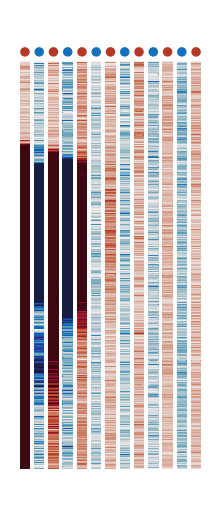

```mathematica
Show[chiralRepresentation,Graphics[graphicsPrimitivesMixedData]]
```

### All the dataset

Comment/uncomment according to the path chosen (see above)

```mathematica
(*pathEXP*)
(*perturbedNodes={"N1","N2","N3","N4","N5","N6","N7"};*)
(*pathEXP2*)
perturbedNodes={"N1","N2","N3","N4","N5","N6","N7","N8","N9"};
(*pathFEM*)
(*perturbedNodes={"N1","N2","N3","N4","N5","N6","N7"};*)
(*pathFEM4*)
(*perturbedNodes={"N16"};*)
(*pathFEM5*)
(*perturbedNodes={"N2","N3","N4","N5","N6","N7","N8","N9","N10","N11","N12"};*)
```

Determine all the displacements and elongations

```mathematica
displacementDataList=Table[With[{data=Import[path[node],"Data"]},
#ᵀ&/@(dataᵀ[[2;;,All,2;;]])],{node,perturbedNodes}];
elongationDataList=Table[Table[Norm[(positionsBeads[[i+1]]+#[[i+1]])-(positionsBeads[[i]]+#[[i]])]-Norm[positionsBeads[[i+1]]-positionsBeads[[i]]],{i,1,nBeads-1}]&/@displacementDataList[[j]],{j,1,Length@perturbedNodes}];
```

## Processing the data

### Displacements and elongations

```mathematica
normDispList=Norm@#&/@#&/@#&/@displacementDataList;
```

```mathematica
node=5;
barl=BarLegend[{viridisCM[#]&,{1,7}},5,LegendLabel->"Node number",LabelStyle->Directive[Black,FontSize->14]];
axesl={"t (ms)","|Displacement| (mm)"};
plotLabel="Perturbation on node "<>ToString[node];
ListPlot[With[{tRange=dt Range[0,Length[normDispList[[node]]]-1]},{tRange,#}ᵀ&/@(normDispList[[node]]ᵀ)],Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLegends->barl,FrameLabel->axesl,PlotLabel->plotLabel]
```

-Graphics-

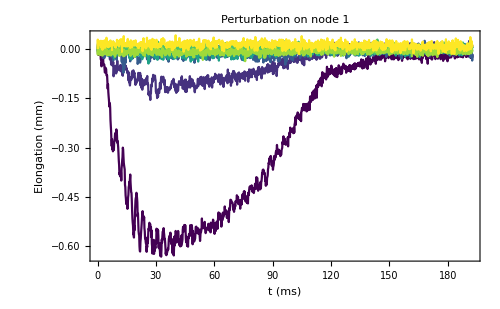

```mathematica
node=1;
barl=BarLegend[{viridisCM[#]&,{1,6}},4,LegendLabel->"Spring number",LabelStyle->Directive[Black,FontSize->14]];
axesl={"t (ms)","Elongation (mm)"};
plotLabel="Perturbation on node "<>ToString[node];
Show[ListPlot[With[{tRange=dt Range[0,Length[elongationDataList[[node]]]-1]},{tRange,#}ᵀ&/@(elongationDataList[[node]]ᵀ)],Evaluate[optionsListPlot],PlotStyle->colorSprings,FrameLabel->axesl,PlotLabel->plotLabel],PlotLegends->barl]
```

#### Mixed data representation

```mathematica
chiralRepresentation=With[{radius=10},
Graphics[{balanceRedColorMap[0.6],Disk[{#1,2radius},radius]&/@positionsBeads[[All,1]],
balanceBlueColorMap[0.6],Disk[{#1,2radius},radius]&/@positionsElongations[[All,1]]}]];
```

```mathematica
iNodeBulk=2;
iNodeFM=5;
radius=10;
thickness=0.1;
maxBulk=Max[normDispList[[iNodeBulk]]];
maxFM=Max[normDispList[[iNodeFM]]];
threshold=0.04;
nData=1000;
bulkInitialIndex=FirstPosition[normDispList[[iNodeBulk]],x_/;x>threshold][[1]];
fmInitialIndex=FirstPosition[normDispList[[iNodeFM]],x_/;x>threshold][[1]];

graphicsPrimitivesMixedDataBulk=Table[Flatten[{MapThread[{balanceRedColorMap[#2/maxBulk],Rectangle[{#1-radius,(-i+bulkInitialIndex-1)thickness},{#1+radius,(-i+bulkInitialIndex-2)thickness}]}&,{positionsBeads[[All,1]],normDispList[[iNodeBulk]][[i]]}],
MapThread[{balanceBlueColorMap[#2/maxBulk],Rectangle[{#1-radius,(-i+bulkInitialIndex-1)thickness},{#1+radius,(-i+bulkInitialIndex-2)thickness}]}&,{positionsElongations[[All,1]],Abs[elongationDataList[[iNodeBulk]]][[i]]}]},1]
,{i,bulkInitialIndex,bulkInitialIndex+nData}];

graphicsPrimitivesMixedDataFM=
Table[Flatten[{MapThread[{balanceRedColorMap[#2/maxFM],Rectangle[{#1-radius,(-i+fmInitialIndex-1)thickness},{#1+radius,(-i+fmInitialIndex-2)thickness}]}&,{positionsBeads[[All,1]],normDispList[[iNodeFM]][[i]]}],
MapThread[{balanceBlueColorMap[#2/maxFM],Rectangle[{#1-radius,(-i+fmInitialIndex-1)thickness},{#1+radius,(-i+fmInitialIndex-2)thickness}]}&,{positionsElongations[[All,1]],Abs[elongationDataList[[iNodeFM]]][[i]]}]},1]
,{i,fmInitialIndex,fmInitialIndex+nData}];
```

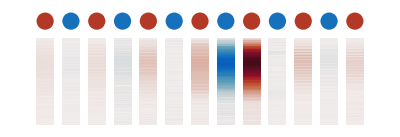

```mathematica
Show[chiralRepresentation,Graphics[graphicsPrimitivesMixedDataFM]]
```

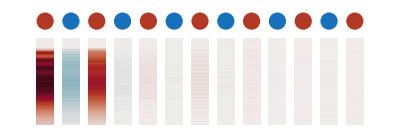

```mathematica
Show[chiralRepresentation,Graphics[graphicsPrimitivesMixedDataBulk]]
```

### Moments

#### Normalized moments and spreading

```mathematica
positionsBeadsExtended=Flatten[ConstantArray[#,2]&/@positionsBeads,1];
flatDisplacementDataList=Map[Flatten[#]&,displacementDataList,{2}];
momentsList=Quiet@MapThread[MapThread[With[{norm2=(#1*.#1+#2*.#2)},
{
Sqrt[norm2],
(#1*.#1-#2*.#2)/norm2,
1/norm2(#1*.(positionsBeadsExtended[[All,1]]#1)+#2*.(positionsElongations[[All,1]]#2)),
1/norm2(#1*.(positionsBeadsExtended[[All,2]]#1)+#2*.(positionsElongations[[All,2]]#2)),
1/norm2(#1*.(positionsBeadsExtended[[All,1]]#1)-#2*.(positionsElongations[[All,1]]#2)),
1/norm2(#1*.(positionsBeadsExtended[[All,2]]#1)-#2*.(positionsElongations[[All,2]]#2))
}]&,{#1,#2}]&,{flatDisplacementDataList,elongationDataList}];
spreadingList=Quiet@MapThread[MapThread[With[{norm2=(#1*.#1+#2*.#2)},
{
Sqrt[norm2],
Sqrt[1/norm2(#1*.(positionsBeadsExtended[[All,1]]^2#1)+#2*.(positionsElongations[[All,1]]^2#2))-1/norm2^2(#1*.(positionsBeadsExtended[[All,1]]#1)+#2*.(positionsElongations[[All,1]]#2))^2],
Sqrt[1/norm2(#1*.(positionsBeadsExtended[[All,2]]^2#1)+#2*.(positionsElongations[[All,2]]^2#2))-1/norm2^2(#1*.(positionsBeadsExtended[[All,2]]#1)+#2*.(positionsElongations[[All,2]]#2))^2]
}]&,{#1,#2}]&,{flatDisplacementDataList,elongationDataList}];
confidence=0.95;
quantileList=Quiet@MapThread[MapThread[
With[{dataX=Sort[{positionsBeads[[All,1]],(Norm@#&/@(#1))^2}ᵀ~Join~({positionsElongations[[All,1]],(Abs@#2)^2}ᵀ)],
dataY=Sort[{positionsBeads[[All,2]],(Norm@#&/@(#1))^2}ᵀ~Join~({positionsElongations[[All,2]],(Abs@#2)^2}ᵀ)]},
{
Quantile[WeightedData@@(dataXᵀ),{(1-confidence)/2,(1+confidence)/2}],
Quantile[WeightedData@@(dataYᵀ),{(1-confidence)/2,(1+confidence)/2}]
}]&,{#1,#2}]&,{displacementDataList,elongationDataList}];
```

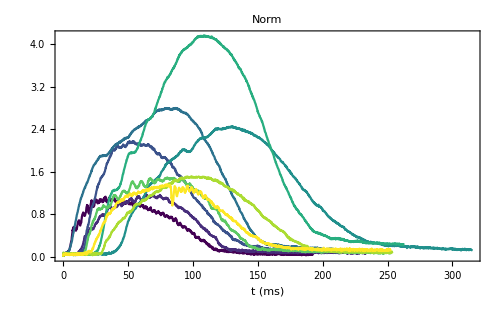
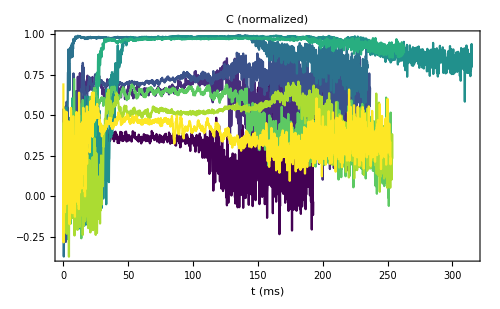
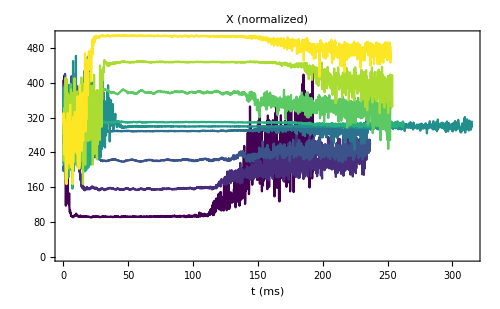
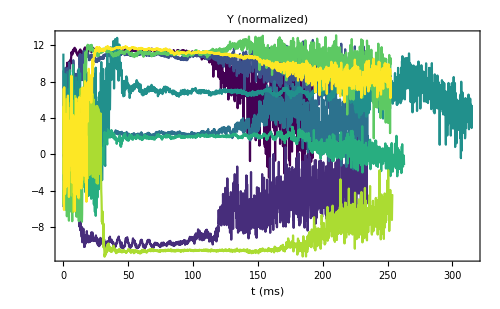
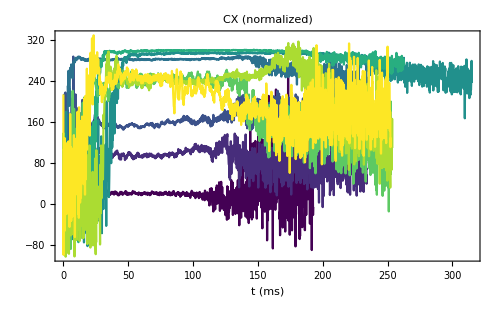
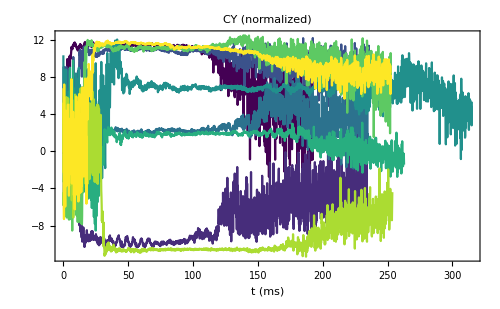

```mathematica
labelPlots={"Norm","C (normalized)", "X (normalized)", "Y (normalized)", "CX (normalized)", "CY (normalized)"};
axesl={"t (ms)",None};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(momentsList[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[6]
```

#### Filter data according to norm

```mathematica
pickList=(#>threshold&/@(#[[All,1]]))&/@momentsList;
momentsList=MapThread[Pick[#1,#2]&,{momentsList,pickList}];
spreadingList=MapThread[Pick[#1,#2]&,{spreadingList,pickList}];
quantileList=MapThread[Pick[#1,#2]&,{quantileList,pickList}];
```

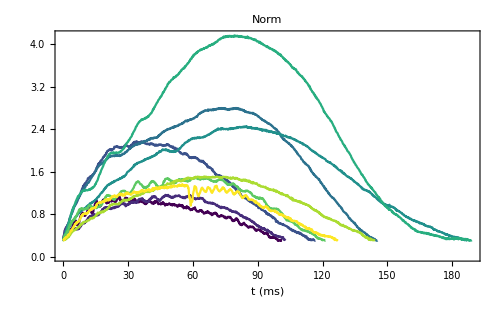
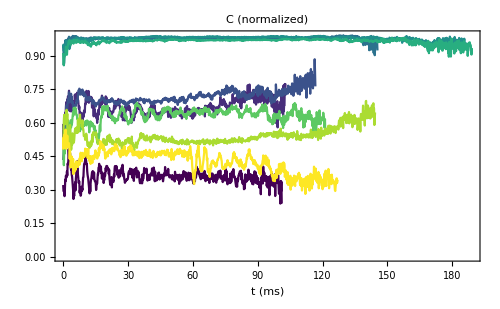
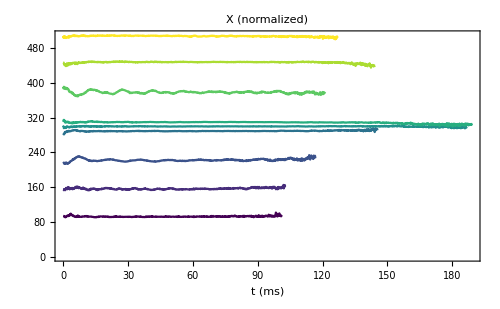
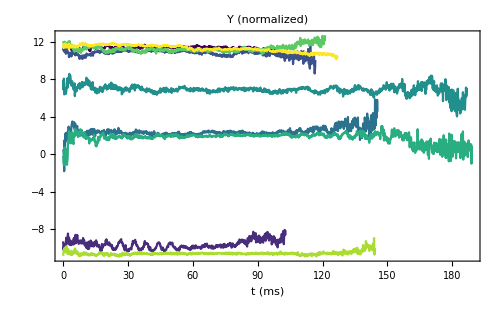
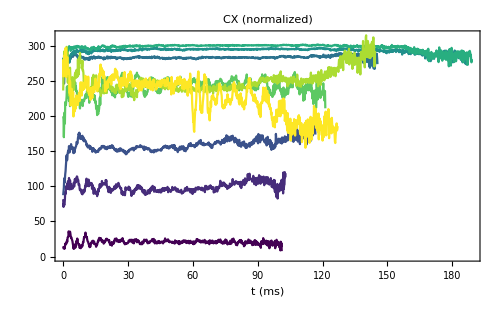
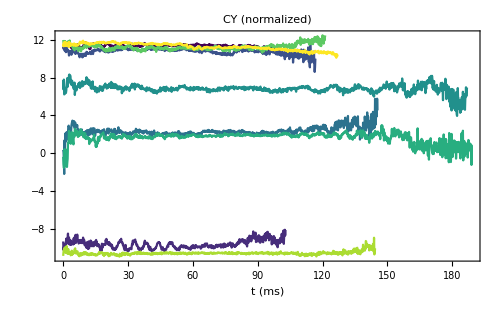

```mathematica
labelPlots={"Norm","C (normalized)", "X (normalized)", "Y (normalized)", "CX (normalized)", "CY (normalized)"};
axesl={"t (ms)",None};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(momentsList[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[6]
```

#### Field time data

```mathematica
fieldTimeData=Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList,{2}];
```

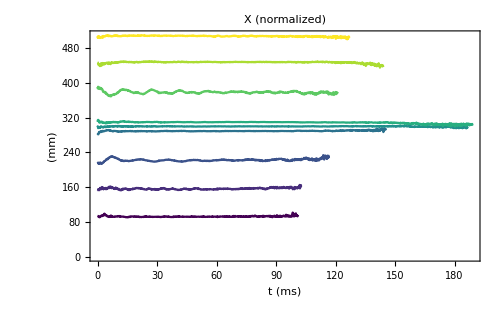
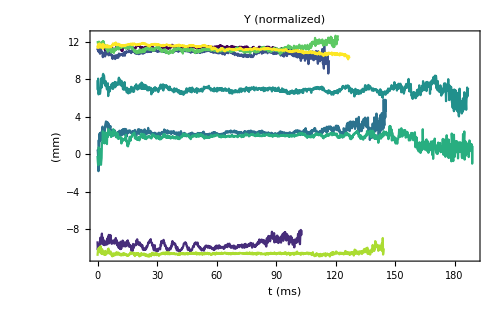
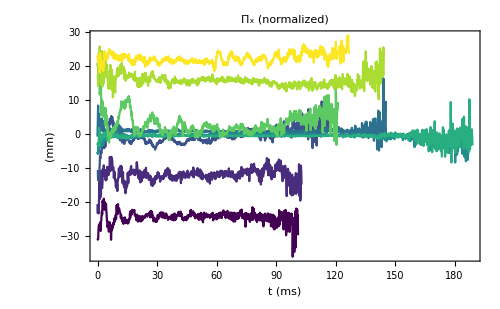
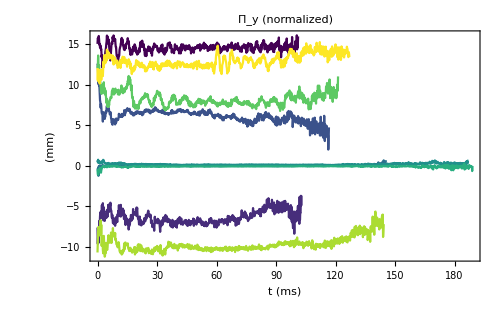

```mathematica
labelPlots={ "X (normalized)", "Y (normalized)", "Π_x (normalized)", "Π_y (normalized)"};
axesl={"t (ms)","(mm)"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(fieldTimeData[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[4]
```

#### Centers

Using Quantiles

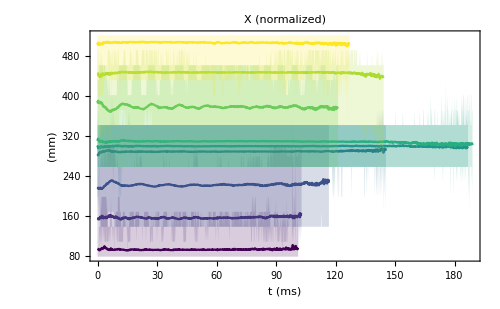

```mathematica
centersAndQuantileTimeData=MapThread[{{dt Range[0,Length[#1]-1],#1}ᵀ,{dt Range[0,Length[#1]-1],#2[[All,1]]}ᵀ,{dt Range[0,Length[#1]-1],#2[[All,2]]}ᵀ}&,{fieldTimeData[[All,All,1]],quantileList[[All,All,1]]}];
Show[ListPlot[centersAndQuantileTimeData[[#]],Filling ->{1->{2},1->{3}},Evaluate[optionsListPlot],PlotStyle->{colorPerturbations[[#]],None,None},PlotLabel->labelPlots[[1]],FrameLabel->axesl]&/@Range[Length@centersAndQuantileTimeData],PlotRange->All]
```

#### Time averages

```mathematica
increasingAverageList[l_List]:=Module[{previous,current},previous=0;Table[current=(previous (i-1)+l[[i]])/i;previous=current;current,{i,1,Length@l}]]
```

```mathematica
iFrame=1;
timeAverageDataList=increasingAverageList[#]&/@(fieldTimeData[[All,iFrame;;,#]])&/@Range[4];
```

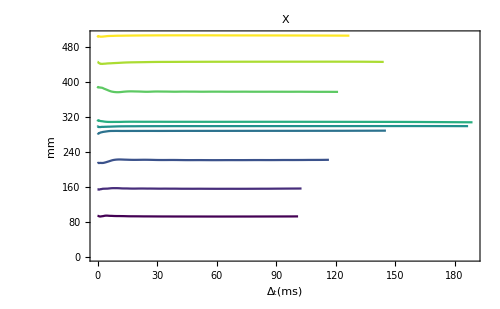
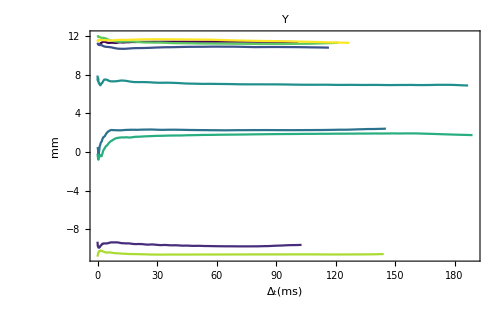
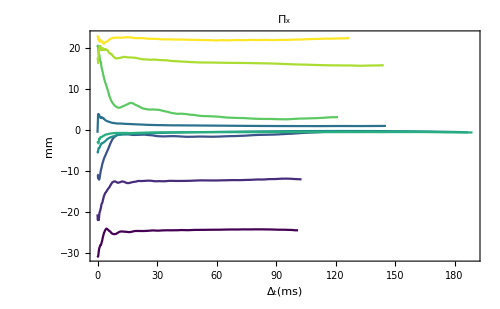
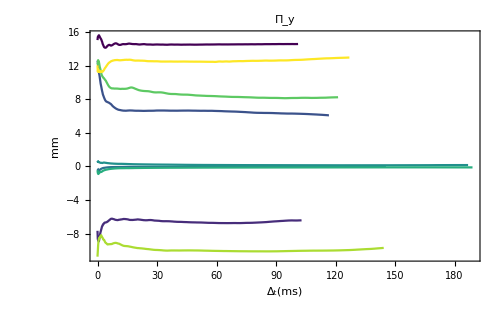

```mathematica
labelPlots={"X","Y","Π_x","Π_y"};
axesl={"Δ_t(ms)","mm"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(timeAverageDataList[[#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,FrameLabel->axesl,PlotLabel->labelPlots[[#]]]&/@Range[4]
```

Comment/uncomment according to the path chosen (see above)

```mathematica
(*EXP*)
(*nFramesAverage=Floor[80/dt];*)
(*EXP2*)
nFramesAverage=Floor[80/dt];
(*FEM*)
(*nFramesAverage=Floor[5/dt];*)
(*FEM3*)
(*nFramesAverage=Floor[5/dt];*)
(*FEM5*)
(*nFramesAverage=Floor[2/dt];*)
```

```mathematica
meanAroundDataList=MeanAround[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
meanDataList=Mean[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
stdDataList=StandardDeviation[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
(*Attention: this is the angle of the means*)
meanAroundAngleList=ArcTan@@#&/@(meanAroundDataList[[3;;4]]ᵀ);
```

```mathematica
meanAngleList=ArcTan@@#&/@(meanDataList[[{3,4}]]ᵀ);
dfdx[x_,y_]=D[ArcTan[x,y], x];
dfdy[x_,y_]=D[ArcTan[x,y], y];
stdAngleList=MapThread[Sqrt[((dfdx@@#1)#2[[1]])^2+((dfdy@@#1)#2[[2]])^2]&,{meanDataList[[{3,4}]]ᵀ,stdDataList[[{3,4}]]ᵀ}];
```

### Graphics

#### 1D vector representation

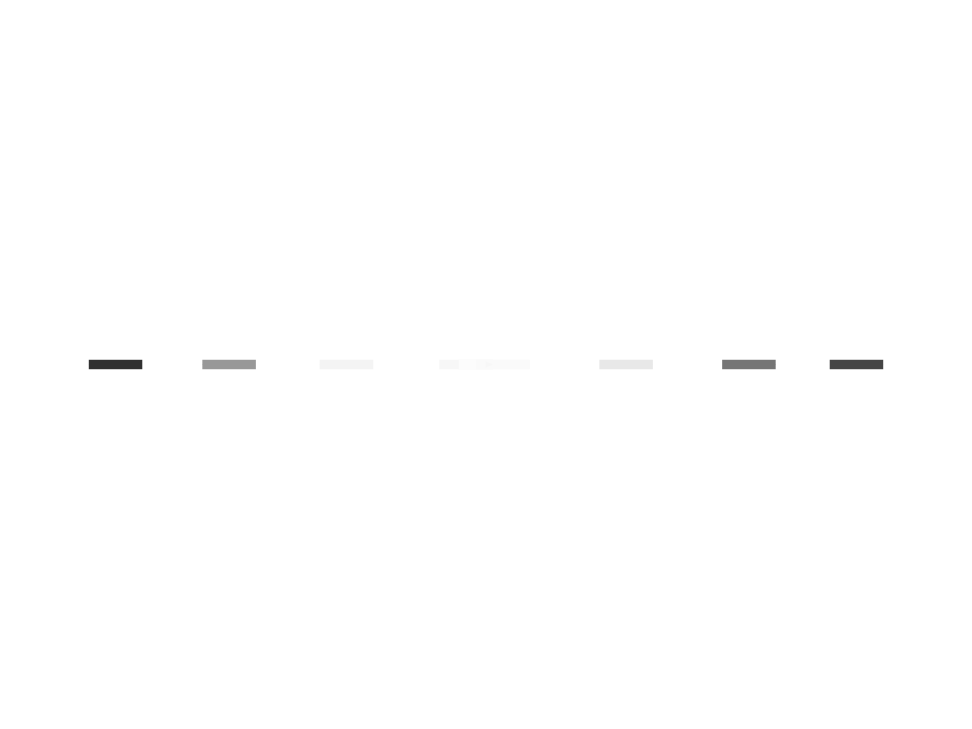

```mathematica
arrowSize=30;
fcolor=GrayLevel[(arrowSize-#)/arrowSize]&;
Graphics[MapThread[{fcolor[Norm@#2],Thickness[0.007],Arrowheads[.03],Arrow[{{#1-Sign[#2]arrowSize/2,0},{#1+Sign[#2]arrowSize/2,0}}]}&,meanDataList[[{1,3}]]]]
```